```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=-f2[r,θ]*r^2*Sin[θ]^2W[r,θ];
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_] := R - a^2/RH;
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coords[[k]]]+D[metric[[s,k]],coords[[j]]]-D[metric[[j,k]],coords[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
riemann:=riemann=Simplify[Table[D[christoffel[[i,j,l]],coords[[k]]]-D[christoffel[[i,j,k]],coords[[l]]]+Sum[christoffel[[s,j,l]] christoffel[[i,k,s]]-christoffel[[s,j,k]] christoffel[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
f0[r_,t_]:=  1/f2[r,t] 
H[r_]:=1-rh/r;
f1[r_,θ_]:=   (1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2   ;
f2[r_,θ_]:=  1/((1-ct/r)^2+(ct (ct-rh) Cos[θ]^2)/r^2)(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);

W[r_,θ_]:=  (1-ct/r)/r^3(√(ct (ct-rh))(rh-2 ct))/(( (1-ct/r)^2+ (ct (ct-rh))/r^2)^2 +ct (rh-ct)(1-rh/r) Sin[θ]^2/r^2);
```

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]] ricci[[i,j]],{i,1,n},{j,1,n}]]
```

0

```mathematica
einstein:=einstein=Simplify[ricci-(1/2) scalar*metric]
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.01*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler 
I want to plot in the R, i.e. BL, radial coordinates, so for solution 1, I have to translate to R via r = R - a^2/RH *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/RH) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/RH) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/RH) Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
τend=.;uinvar = 0;
rh=1.0;ct=-0.05;
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2/M
RH = M+Sqrt[M^2-a^2];
(* Since we are plotting in the BL space, the horizon is at RH, not rh *)
horizpl=PolarPlot[RH,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
τPlot=100;
```

0.55

0.229129

```mathematica
soln=computeSoln[τPlot,{-0.1,0,0.01},{0,Rtor[8 RH],π/2,0}];
xyzsoln=sphslnToCartsln[soln];
Table[{τi,coords[[2]][τ] /. soln /. τ -> τi},{τi,0,100,1}]
```

{{0,{8.35+0. ⅈ}},{1,{8.25034+0. ⅈ}},{2,{8.15139+0. ⅈ}},{3,{8.05316+0. ⅈ}},{4,{7.95569+0. ⅈ}},{5,{7.85899+0. ⅈ}},{6,{7.76309+0. ⅈ}},{7,{7.66802+0. ⅈ}},{8,{7.57382+0. ⅈ}},{9,{7.4805+0. ⅈ}},{10,{7.3881+0. ⅈ}},{11,{7.29665+0. ⅈ}},{12,{7.20619+0. ⅈ}},{13,{7.11674+0. ⅈ}},{14,{7.02835+0. ⅈ}},{15,{6.94104+0. ⅈ}},{16,{6.85487+0. ⅈ}},{17,{6.76985+0. ⅈ}},{18,{6.68605+0. ⅈ}},{19,{6.60348+0. ⅈ}},{20,{6.52221+0. ⅈ}},{21,{6.44227+0. ⅈ}},{22,{6.36371+0. ⅈ}},{23,{6.28656+0. ⅈ}},{24,{6.21089+0. ⅈ}},{25,{6.13674+0. ⅈ}},{26,{6.06415+0. ⅈ}},{27,{5.99318+0. ⅈ}},{28,{5.92388+0. ⅈ}},{29,{5.85629+0. ⅈ}},{30,{5.79048+0. ⅈ}},{31,{5.7265+0. ⅈ}},{32,{5.6644+0. ⅈ}},{33,{5.60423+0. ⅈ}},{34,{5.54605+0. ⅈ}},{35,{5.48992+0. ⅈ}},{36,{5.43588+0. ⅈ}},{37,{5.384+0. ⅈ}},{38,{5.33433+0. ⅈ}},{39,{5.28692+0. ⅈ}},{40,{5.24182+0. ⅈ}},{41,{5.19909+0. ⅈ}},{42,{5.15877+0. ⅈ}},{43,{5.12092+0. ⅈ}},{44,{5.08558+0. ⅈ}},{45,{5.0528+0. ⅈ}},{46,{5.02261+0. ⅈ}},{47,{4.99507+0. ⅈ}},{48,{4.9702+0. ⅈ}},{49,{4.94804+0. ⅈ}},{50,{4.92863+0. ⅈ}},{51,{4.91198+0. ⅈ}},{52,{4.89812+0. ⅈ}},{53,{4.88708+0. ⅈ}},{54,{4.87887+0. ⅈ}},{55,{4.87349+0. ⅈ}},{56,{4.87097+0. ⅈ}},{57,{4.8713+0. ⅈ}},{58,{4.87448+0. ⅈ}},{59,{4.88051+0. ⅈ}},{60,{4.88937+0. ⅈ}},{61,{4.90107+0. ⅈ}},{62,{4.91557+0. ⅈ}},{63,{4.93285+0. ⅈ}},{64,{4.9529+0. ⅈ}},{65,{4.97569+0. ⅈ}},{66,{5.00118+0. ⅈ}},{67,{5.02933+0. ⅈ}},{68,{5.06012+0. ⅈ}},{69,{5.0935+0. ⅈ}},{70,{5.12942+0. ⅈ}},{71,{5.16784+0. ⅈ}},{72,{5.20872+0. ⅈ}},{73,{5.252+0. ⅈ}},{74,{5.29763+0. ⅈ}},{75,{5.34557+0. ⅈ}},{76,{5.39576+0. ⅈ}},{77,{5.44814+0. ⅈ}},{78,{5.50266+0. ⅈ}},{79,{5.55927+0. ⅈ}},{80,{5.61791+0. ⅈ}},{81,{5.67853+0. ⅈ}},{82,{5.74107+0. ⅈ}},{83,{5.80548+0. ⅈ}},{84,{5.87171+0. ⅈ}},{85,{5.93969+0. ⅈ}},{86,{6.00938+0. ⅈ}},{87,{6.08073+0. ⅈ}},{88,{6.15368+0. ⅈ}},{89,{6.22819+0. ⅈ}},{90,{6.30421+0. ⅈ}},{91,{6.38168+0. ⅈ}},{92,{6.46057+0. ⅈ}},{93,{6.54082+0. ⅈ}},{94,{6.62239+0. ⅈ}},{95,{6.70524+0. ⅈ}},{96,{6.78933+0. ⅈ}},{97,{6.87462+0. ⅈ}},{98,{6.96106+0. ⅈ}},{99,{7.04862+0. ⅈ}},{100,{7.13726+0. ⅈ}}}

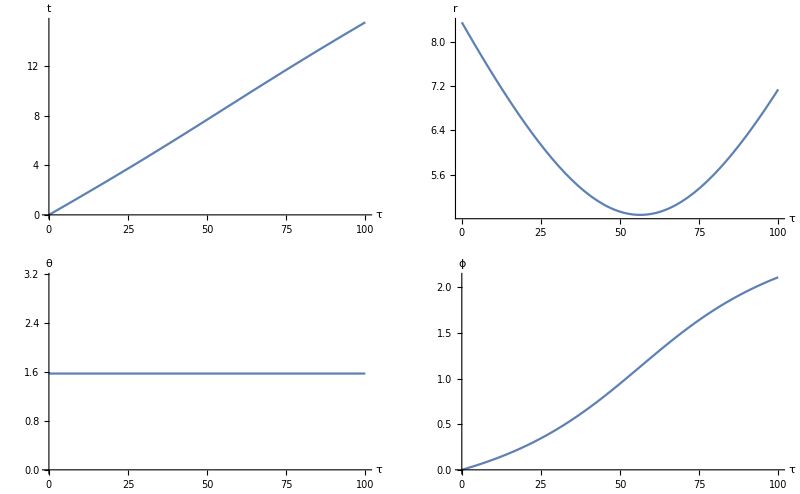

```mathematica
GraphicsGrid[{{Plot[{Evaluate[coords[[1]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","t"}],Plot[{Evaluate[coords[[2]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","r"}]},{Plot[{Evaluate[coords[[3]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","θ"}],Plot[{Evaluate[coords[[4]][τ]/.soln]},{τ,0,τend},AxesLabel->{"τ","ϕ"}]}}]
```

For initial coordinates={0,4.15,π/2,0} and initial velocities={-0.1,0,0.01} the particle crosses the horizon at τend=35.5595

With final coordinates={t = 11.0701 + 0. I,r = 1.01 + 0. I,θ = 1.5708 + 0. I,ϕ = 2.35433 + 0. I}

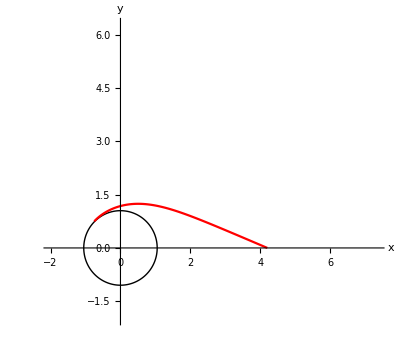

```mathematica
(* first one, in red, is other Kerr and the second one, in blue, is BL Kerr *)
genXYPlot[τPlot,{0,Rtor[4 RH],π/2,0},{-0.1,0,0.01},1];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-2,7RH},{-2,6RH}}]
```

```mathematica
(* other coords *)
Print["a=",a,", M=",M,", rh=",rh,", ct=",ct]
r0 = 50;
NumberForm[tt/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[rr/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[θθ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[ϕϕ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[tϕ/.r->Rtor[r0]/.θ->π/2,16];
NumberForm[christoffel[[1,1,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[2,2,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[1,1,1]]  /. r-> Rtor[r0] /. θ -> π/2,16]
NumberForm[christoffel[[3,2,2]]  /. r-> Rtor[r0] /. θ -> π/2,16]
```

a=0.229129, M=0.55, rh=1., ct=-0.05

0.0002249487689937128

-0.0002245146065370784

0.

0.